```mathematica
(*
1. Data backup.
2. Preserve this code: valid for Tanay-Stein-Ghersi 1.5PN paper with σ1=(1+(3/4) (m2/m1))  σ2=(1+(3/4)  (m1/m2)).
3. Racine, Gerosa: Re-interpretation of Seff.L = (σ1 S1 + σ2 S2).L
where
σ1=(1+ m2/m1)  σ2=(1+  m1/m2).

Check with Tom's code.

4. Run the code again. Find new minima.
5. Hopefully, the minima are not at the boundaries of the phase space, i.e. they are crossable. Think of vector rotation schemes which lets us cross the separatrix. Already done before. 
6. Your plan to cross separatrix by keeping Seff.L fixed and changing J by only changing Δϕ does not work if Δϕ is on the boundary (0 or 2 π). So, find a better optimal point for this to work.
7. Or change Seff.L while keeping J constant: rotate S1, S2 about S = S1+S2.

8. If these don't work: Hunt for minima using ContourPlot3D(3 angle space) or ContourPlot(2 (J, Seff.L) space); example below. Advantage: you simply need to cross this boundary without keeping J or SeffdL constants (i.e. moving horizontally/vertically only). Hence more freedom in perturbing the optimal configuration.

9. Evolve system on these 2 points straddling the separatrix: hopefully they diverge at some point.
*)
```

```mathematica
(*ContourPlot[x^2+ y^2==1,{x,-1.5,1.5}, {y,0,1}]
ContourPlot3D[x^2+ y^2 +z^2==1,{x,-1.5,1.5}, {y,0,1}, {z,0,1}]*)
```

```mathematica
L=0.7;
S1=0.3  ;
S2=0.4 ;
```

If m_1,m_2>0 and m_1>m_2, then 0<σ_1<1.75

```mathematica
σ1=1.5   ; (*σ1=1.5*)
0<σ<1.75/.σ->σ1
```

True

### Parameter definitions

```mathematica
Δ1 = ((J^2-L^2-S1^2-S2^2)/2  -   SeffdL/σ2)/(σ1-σ2);
Δ2 = ((J^2-L^2-S1^2-S2^2)/2  -   SeffdL/σ1)/(σ1-σ2);
σ2 = 1+1/(-1+σ1)   ;

(*σ1=(1+ m2/m1)  σ2=(1+  m1/m2)*)
(* Not this σ1=(1+3/4 m2/m1)  σ2=(1+3/4  m1/m2)*)
```

### Cubic function roots

```mathematica
cubic =    Expand[ L^2 S1^2 S2^2- 2 σ1 σ2 (σ1-σ2)f(f-Δ1)(f-Δ2)-L^2(σ1-σ2)^2 f^2-S2^2 σ2^2(f-Δ1)^2-S1^2 σ1^2(f-Δ2)^2  ] (*The cubic polynomial of Eq. 3.1 of Cho-Lee*);
a3=Coefficient[cubic,f^3];
a2=Coefficient[cubic,f^2];
a1=Coefficient[cubic,f];
a0=Expand[cubic-(a3 f^3+a2 f^2+a1 f)];
p=(3 a1 a3-a2^2)/(3 a3^2);
q=(2 a2^3-9a1 a2 a3+27a0 a3^2)/(27 a3^3);
roots=Table[Subscript[f, k]->-a2/(3a3)+2 √(-p/3)Cos[1/3 ArcCos[(3q)/(2p)√(-3/p)]+(2π k)/3],{k,1,3}];
f1=roots[[1,2]];
f2=roots[[2,2]];
f3=roots[[3,2]];
```

### Flow amounts definitions

```mathematica
(*The following definitions are in Cho-Lee*)
```

#### Δλ_(S_eff.L)

```mathematica
A=  2 σ1 σ2 (σ2-σ1) ;
β=√((f2-f1)/(f3-f1)) (*elliptic modulus "k"*);
Δλ1= 4/(√(A(f3-f1)))EllipticK[β];
```

#### Δλ_(J^2)

```mathematica
B1 = 1/2((SeffdL + L^2(σ1+σ2))(J+L)+ L(σ1 S1^2+σ2 S2^2+(σ1+σ2)(Δ2 σ1-Δ1 σ2))) ;
B2 = 1/2((SeffdL + L^2(σ1+σ2))(J-L)- L(σ1 S1^2+σ2 S2^2+(σ1+σ2)(Δ2 σ1-Δ1 σ2))) ;
D1=L(L+J)+Δ2 σ1-Δ1 σ2;
D2=L(L-J)+Δ2 σ1-Δ1 σ2;
α1 = ((σ1-σ2)(f2-f1))/(D1-f1(σ1-σ2))  ;
α2 = ((σ1-σ2)(f2-f1))/(D2-f1(σ1-σ2))  ;
Δλ2=-1/(2 J) (4/(√(A(f3-f1)))) ((B1  EllipticPi[α1,β^2])/(D1-f1(σ1-σ2))+(B2 EllipticPi[α2,β^2])/(D2-f1(σ1-σ2)));
```

#### Δλ_(L^2)

```mathematica
Δλ3=-1/(2 L)((4/(√(A(f3-f1)))) ((B1  EllipticPi[α1,β^2])/(D1-f1(σ1-σ2))-(B2 EllipticPi[α2,β^2])/(D2-f1(σ1-σ2)))  - (SeffdL +(Δ1-Δ2)σ1 σ2 + L^2(σ1+σ2))Δλ1/L )  ;
```

#### Δλ_(S_1^2)

```mathematica
B1S1= 1/2(-L^2 S1 σ1+J S1^2 σ1-S1^3 σ1-S1 Δ2 σ1^2+J^2 S1 σ2-2 J S1^2 σ2+S1^3 σ2-J Δ1 σ1 σ2+2 S1 Δ1 σ1 σ2+J Δ1 σ2^2-S1 Δ1 σ2^2)  ;
B2S1= 1/2(L^2 S1 σ1+J S1^2 σ1+S1^3 σ1+S1 Δ2 σ1^2-J^2 S1 σ2-2 J S1^2 σ2-S1^3 σ2-J Δ1 σ1 σ2-2 S1 Δ1 σ1 σ2+J Δ1 σ2^2+S1 Δ1 σ2^2)   ;
D1S1=-J S1+S1^2-Δ1 σ2;
D2S1=(J S1+S1^2-Δ1 σ2);

α1S1 = ((-σ1)(f2-f1))/(D1S1+f1 σ1)  ;
α2S1= ((-σ1)(f2-f1))/(D2S1+f1 σ1)  ;
Δλ4=-1/(2 S1)((4/(√(A(f3-f1))))(-(B1S1 EllipticPi[α1S1,β^2])/(D1S1+f1 σ1)+(B2S1 EllipticPi[α2S1,β^2])/(D2S1+f1 σ1))  +  S1(σ2-σ1)Δλ1  )  ;
```

#### Δλ_(S_2^2)

```mathematica
B1S2=1/2(S2 σ2(L^2-J S2+S2^2-Δ1 σ2)-(J-S2)^2 S2 σ1-(J-2S2)Δ2 σ1 σ2+(J-S2)Δ2 σ1^2);
B2S2=1/2(S2 σ2(-L^2-J S2-S2^2+Δ1 σ2)+(J+S2)^2 S2 σ1-(J+2S2)Δ2 σ1 σ2+(J+S2)Δ2 σ1^2);
D1S2=(J-S2)S2-Δ2 σ1;
D2S2=-(J+S2)S2-Δ2 σ1;
α1S2 = ((-σ2)(f2-f1))/(D1S2+f1 σ2)  ;
α2S2= ((-σ2)(f2-f1))/(D2S2+f1 σ2)  ;
Δλ5=-1/(2 S2)((4/(√(A(f3-f1))))(-(B1S2 EllipticPi[α1S2,β^2])/(D1S2+f1 σ2)+(B2S2 EllipticPi[α2S2,β^2])/(D2S2+f1 σ2))  +  S2(σ1-σ2)Δλ1  )  ;
```

### Fifth action J_5

```mathematica
I5=1/π(SeffdL Δλ1+J^2 Δλ2+L^2 Δλ3+S1^2 Δλ4+S2^2 Δλ5);
```

```mathematica
dI5=D[I5,SeffdL];
```

```mathematica
(*(*(*(*(*MinConst=NMinimize[{Abs[1/dI5],J>0,SeffdL>0},{SeffdL,J}]*)*)*)*)*)
```

### Spherical J_5

Assumming  along the  axis, thus

```mathematica
(*SeffdL=σ1 S1dL+σ2 S2dL*)
```

```mathematica
S1dL=S1 L(Cos[θ1] Cos[0]+Sin[θ1] Sin[0] Cos[ϕ1-0])
S2dL=S2 L(Cos[θ2] Cos[0]+Sin[θ2] Sin[0] Cos[ϕ2-0])
S1dS2=S1 S2(Cos[θ1] Cos[θ2]+Sin[θ1] Sin[θ2] Cos[Δϕ])
```

0.21 Cos[θ1]

0.28 Cos[θ2]

0.12 (Cos[θ1] Cos[θ2]+Cos[Δϕ] Sin[θ1] Sin[θ2])

```mathematica
dI5sph=dI5/.{SeffdL->(σ1 S1dL+σ2 S2dL)}/.{J->√(L^2+S1^2+S2^2+2(S1dL+S2dL+S1dS2))};
```

```mathematica
MinAngles=NMinimize[{Abs[1/dI5sph],1<=θ1<= π, 1/5<=θ2<=   π, 1/100<=Δϕ<=  49/100   2 π   (*,(σ1 S1dL+σ2 S2dL)>0*)     },{θ1,θ2,Δϕ}, WorkingPrecision->50, PrecisionGoal->30, MaxIterations->500]
```

NMinimize::precw: The precision of the argument function (Divide[Pi, Abs[Divide[1.08866 EllipticK[Power[Divide[0. - <<8>>7 <<2>> + 0.0493827 <<1>> Sin[Divide[Pi, 6] + Divide[ArcCos[Divide[0.5 <<1>> (2 Power[-9.405 + <<2>>, 3] + <<2>>), -<<1>> + <<1>>]], 3]], <<1>>], <<1>>]], <<1>>] + <<7>>]]) is less than WorkingPrecision (50).

NMinimize::cvmit: Failed to converge to the requested accuracy or precision within 500 iterations.

{2.48348545246778502788758058927517935465800746897×10^-8,{θ1→2.1633271304010700298104388665172387780220694637929,θ2→1.9993555170594953328377411920791409429148636275827,Δϕ→1.3952595200542777618398699237301061156672711450867}}

```mathematica
Jphys=√(L^2+S1^2+S2^2+2(S1dL+S2dL+S1dS2))//.MinAngles[[2]]
```

0.600045

```mathematica
SeffdLphys=(σ1 S1dL+σ2 S2dL)//.MinAngles[[2]]
```

-0.524987

```mathematica
Re[1/dI5/.J->Jphys]/.SeffdL->SeffdLphys
Im[1/dI5/.J->Jphys]/.SeffdL->SeffdLphys
```

-9.14797×10^-8

0

```mathematica
plot3D =Plot3D[Abs[1/dI5] , {J,0.97Jphys, 1.03 Jphys} , {SeffdL , 0.9 SeffdLphys, 1.1 SeffdLphys}]
```

-Graphics3D-

```mathematica
MinAngles[[2]]
```

{θ1→2.1633271304010700298104388665172387780220694637929,θ2→1.9993555170594953328377411920791409429148636275827,Δϕ→1.3952595200542777618398699237301061156672711450867}

```mathematica
MinAnglesPert ={θ1->1.0012 2.16332713040107002981043886651723877802206946379291579050600483745670115250993`50.,θ2->1.003 1.99935551705949533283774119207914094291486362758271432860879472870862789835976`50.,Δϕ->0.99 1.39525952005427776183986992373010611566727114508673385005522725040676978201378`50.};
JphysPert=√(L^2+S1^2+S2^2+2(S1dL+S2dL+S1dS2))//.MinAnglesPert 
SeffdLphysPert=(σ1 S1dL+σ2 S2dL)     //.MinAnglesPert 

verticalLine1=Graphics3D[{Red,Thickness[0.007],Line[{{Jphys,SeffdLphys,-6},{Jphys,SeffdLphys,6}}] }];
verticalLine2=Graphics3D[{Blue,Thickness[0.007],Line[{{JphysPert,SeffdLphysPert,-6},{Jphys,SeffdLphysPert,6}}] }];
Show[plot3D,verticalLine1,verticalLine2]
```

0.599481

-0.530241

-Graphics3D-

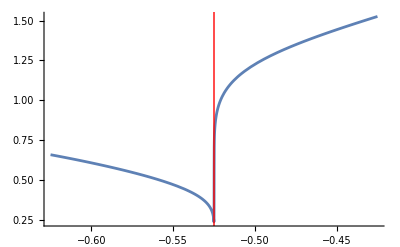

-Graphics-

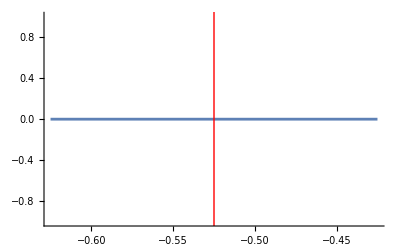

```mathematica
lowLim = SeffdLphys - 0.1; upLim = SeffdLphys + 0.1;
Plot[Abs[1/dI5]/. J->Jphys,{SeffdL,lowLim,upLim},Epilog->{Red,Line[{{SeffdLphys,-10^6},{SeffdLphys,10^6}}]}]
Plot[Re[1/dI5]/. J->Jphys,{SeffdL,lowLim,upLim},Epilog->{Red,Line[{{SeffdLphys,-10^6},{SeffdLphys,10^6}}]}]
Plot[Im[1/dI5]/. J->Jphys,{SeffdL,lowLim,upLim},Epilog->{Red,Line[{{SeffdLphys,-10^6},{SeffdLphys,10^6}}]}]
```

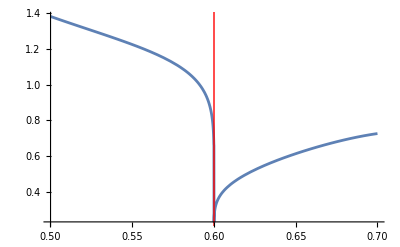

-Graphics-

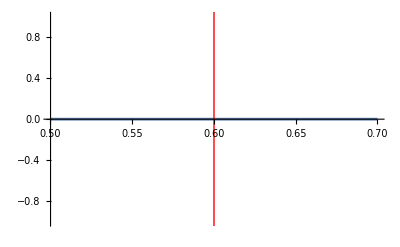

```mathematica
lowLim = Jphys - 0.1; upLim = Jphys + 0.1;
Plot[Abs[1/dI5]/. SeffdL->SeffdLphys,{J,lowLim,upLim},Epilog->{Red,Line[{{Jphys,-10^6},{Jphys,10^6}}]}]
Plot[Re[1/dI5]/. SeffdL->SeffdLphys,{J,lowLim,upLim},Epilog->{Red,Line[{{Jphys,-10^6},{Jphys,10^6}}]}]
Plot[Im[1/dI5]/. SeffdL->SeffdLphys,{J,lowLim,upLim},Epilog->{Red,Line[{{Jphys,-10^6},{Jphys,10^6}}]}]
```

```mathematica
Roots1=roots/.J->Jphys/.SeffdL->SeffdLphys
Roots2=roots/.J->JphysPert/.SeffdL->SeffdLphysPert
```

{f_1→-0.0533435,f_2→0.0799792,f_3→0.0800042}

{f_1→-0.0541179,f_2→0.0776967,f_3→0.080009}

### Spherical to cartesian

```mathematica
CreateVectors[inputArray_]:=Module[{theta1,theta2,deltaPhi,L,S1,S2,LVector,S1Vector,S2Vector,phi1,phi2},(*Extract input values from the array*){theta1,theta2,deltaPhi}=inputArray;
L=7/10;
S1=3/10;
S2=4/10;
phi1=0;
phi2=phi1-deltaPhi;
LVector={0,0,L};
S1Vector={S1 Sin[theta1] Cos[phi1],S1 Sin[theta1] Sin[phi1],S1 Cos[theta1]};
S2Vector={S2 Sin[theta2] Cos[phi2],S2 Sin[theta2] Sin[phi2],S2 Cos[theta2]};
{LVector,S1Vector,S2Vector}]
```

```mathematica
AngleVectors ={θ1,θ2, Δϕ}/.     {θ1->10112/10000* 2.16332713040107002981043886651723877802206946379291579050600483745670115250993`50.,θ2->1013/1000* 1.99935551705949533283774119207914094291486362758271432860879472870862789835976`50.,Δϕ->99/100* 1.39525952005427776183986992373010611566727114508673385005522725040676978201378`50.} ;
VectorVector =CreateVectors[AngleVectors]
```

{{0,0,7/10},{0.2447270089155180138147783168089598042803705133683,0,-0.173518561275916434967755870173052679274194346636},{0.06769253257329271044828683627661085535452631694402,-0.3529505671765900077074676087961110362782109061952,-0.1756235125589313842533858384639796731520814453385}}

### System equations

```mathematica
Clear[S1,S2,L,J]
```

```mathematica
m1 = 1;
m2 = 1/2 ;
```

Recall that m_1>m_2

```mathematica
d=1;
M=m1+m2;
μ =  (m1 m2)/M ;
q = m1/m2 ;
```

```mathematica
{Linit, S1init, S2init}=VectorVector
S0= (1+m2/m1)S1[t]+(1+m1/m2)S2[t] ;
S = S1[t]+S2[t];
λ = ((1+m2/m1)L[t].S1[t]+(1+m1/m2)L[t].S2[t])/Norm[L[t]]^2;

sol0 = NDSolve[{S1'[t]==1/(2 d^3) Cross[(4 + 3 m2/m1 - 3 μ/m1 λ )L[t]+S2[t], S1[t]] ,S2'[t]==1/(2 d^3) Cross[(4 + 3 m1/m2 - 3 μ/m2 λ )L[t]+S1[t], S2[t]],
L'[t]==1/(2 d^3) Cross[ S +3 (1-μ/M λ)S0, L[t]], S1[0]==S1init , S2[0]==S2init,  L[0]==Linit},  {S1,S2,L},{t,0,80}];
```

{{0,0,7/10},{0.2447270089155180138147783168089598042803705133683,0,-0.173518561275916434967755870173052679274194346636},{0.06769253257329271044828683627661085535452631694402,-0.3529505671765900077074676087961110362782109061952,-0.1756235125589313842533858384639796731520814453385}}

```mathematica
S1v=(S1 /.sol0[[1]])  ;
S2v=(S2 /.sol0[[1]])   ;
Lv=(L /.sol0[[1]])  ;
```

```mathematica
Plot[{S1v[t].S2v[t],S1v[t].Lv[t],S2v[t].Lv[t]}  , {t,0,80},PlotLegends->Automatic]
```

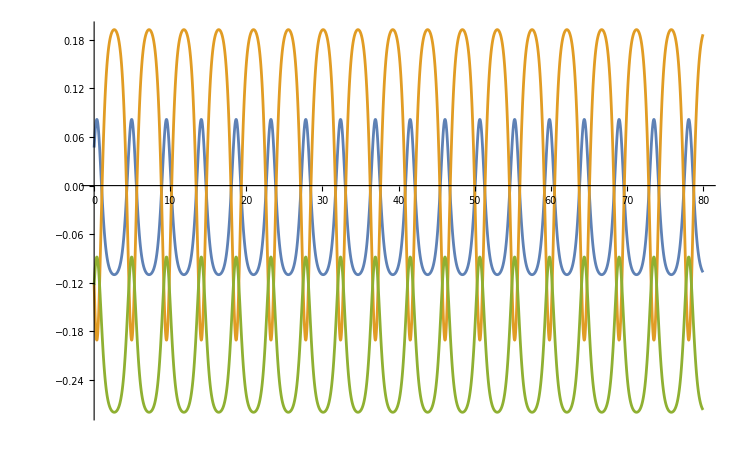

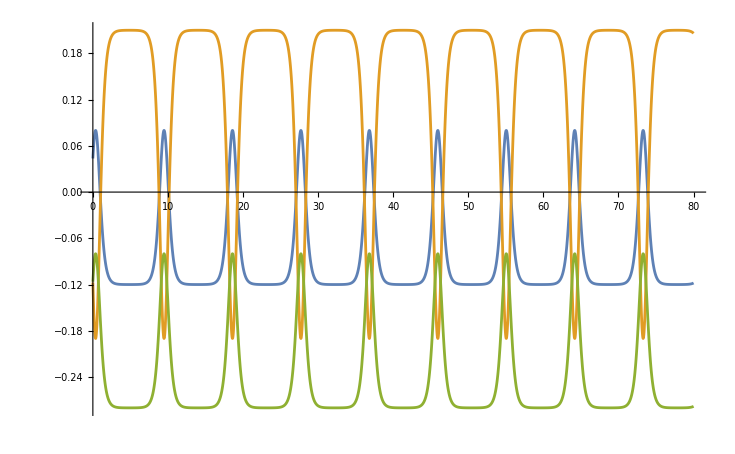

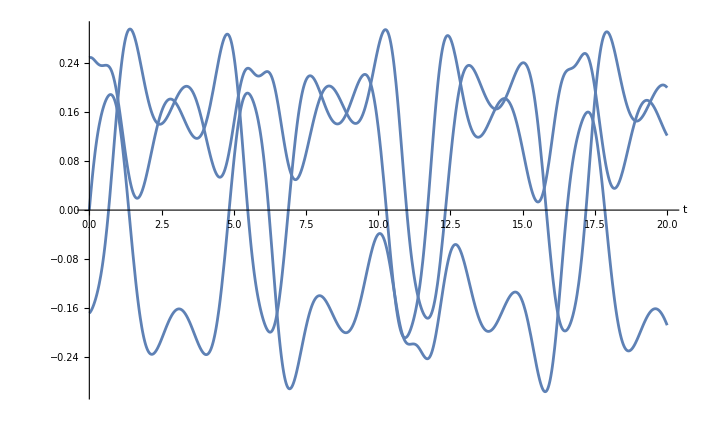

```mathematica
Plot[S1v[t] , {t,0,20},AxesLabel->{"t",""}]
```

```mathematica
S10=S1init;
S20=S2init;
L0=Linit;
J0=S10+S20+L0;
```

```mathematica
ξ0=1/M^2 Dot[((1+1/q)S10+(1+q)S20),L0/Norm[L0]]
```

-0.3333248231775557535062365029471967392606093811904

```mathematica
normrules={J->Norm[J0],L->Norm[L0],S1->Norm[S10],S2->Norm[S20]}//N
```

{J→0.600045,L→0.7,S1→0.3,S2→0.4}

```mathematica
J>S1+S2-L//.normrules
Smin=Max[Abs[J-L],Abs[S1-S2]]//.normrules
Smax=Min[J+L,S1+S2]//.normrules
```

True

0.1

0.7

```mathematica
Clear[S]
```

```mathematica
ξmax=1/(4 L M^2 q S^2)((J^2-L^2-S^2) ((1+q)^2 S^2-(1-q^2) (S1^2-S2^2))-(1-q^2) √(J^2-(L-S)^2) √(-J^2+(L+S)^2) √(S^2-(S1-S2)^2) √(-S^2+(S1+S2)^2) Cos[ϕ])//.normrules/.S->Smin
ξmin=1/(4 L M^2  q S^2)((J^2-L^2-S^2) ((1+q)^2 S^2-(1-q^2) (S1^2-S2^2))-(1-q^2) √(J^2-(L-S)^2) √(-J^2+(L+S)^2) √(S^2-(S1-S2)^2) √(-S^2+(S1+S2)^2) Cos[ϕ])//.normrules/.S->Smax
```

0.133282

-0.421732

```mathematica
ContξSp=1/(4 L M^2 q S^2)((J^2-L^2-S^2) ((1+q)^2 S^2-(1-q^2) (S1^2-S2^2))-(1-q^2) √(J^2-(L-S)^2) √(-J^2+(L+S)^2) √(S^2-(S1-S2)^2) √(-S^2+(S1+S2)^2) Cos[ϕ])//.normrules/.Cos[ϕ]->-1//FullSimplify
ContξSm=1/(4 L M^2 q S^2)((J^2-L^2-S^2) ((1+q)^2 S^2-(1-q^2) (S1^2-S2^2))-(1-q^2) √(J^2-(L-S)^2) √(-J^2+(L+S)^2) √(S^2-(S1-S2)^2) √(-S^2+(S1+S2)^2) Cos[ϕ])//.normrules/.Cos[ϕ]->+1//FullSimplify
```

(0.00216577-0.0761522 S^2-0.714286 S^4-0.238095 √(-0.129946-1. (-1.4+S) S) √(-0.0049+0.5 S^2-1. S^4) √(0.129946+S (1.4+S)))/S^2

(0.00216577-0.0761522 S^2-0.714286 S^4+0.238095 √(-0.129946-1. (-1.4+S) S) √(-0.0049+0.5 S^2-1. S^4) √(0.129946+S (1.4+S)))/S^2

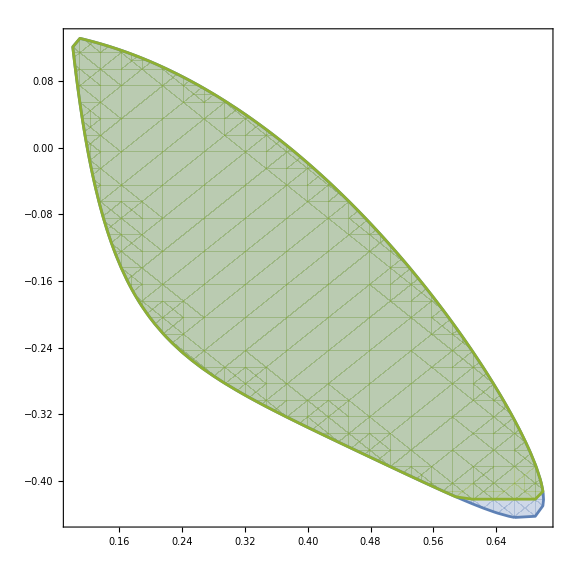

```mathematica
TheEgg=RegionPlot[{ξ<ContξSm&&ξ>ContξSp&&ξ<ξmax,ξ<ContξSm&&ξ>ContξSp&&ξ>ξmax,ξ<ContξSm&&ξ>ContξSp&&ξmin<ξ<ξmax},{S,Smin-0.2,Smax+0.2},{ξ,ξmin-0.1,ξmax+0.1},PlotRange->{All,All},ImageSize->Large]
```

```mathematica
NormS0[t_]:=Norm[S1v[t]+S2v[t]];
```

```mathematica
Manipulate[Show[TheEgg,Graphics[{PointSize[0.015],Black,Point[{NormS0[t],ξ0}]}],PlotRange->All,Frame->True,FrameLabel->{Style["S(t)",15,Black],Style["ξ",15,Black]},FrameStyle->Directive[15,Black]],{t,0,0.5}]
```

```mathematica
A1=(J^2-(L-S)^2)^(1/2);
A2=((L+S)^2-J^2)^(1/2);
A3=(S^2-(S1-S2)^2)^(1/2);
A4=((S1+S2)^2-S^2)^(1/2);
```

```mathematica
Simplify[((J^2-L^2-S^2)(S^2(1+q)^2-(S1^2-S2^2)(1-q^2))-(1-q^2)A1 A2 A3 A4 Cos[ϕ])/(4q M^2 S^2 L)/.S1->Norm[S10]/.S2->Norm[S20]/.L->Norm[L0]/.J->Norm[J0]]
```

1/S^2(0.0021657737272126763580658023805609767722461568944-0.076152207356733748679010578214518052143882914523 S^2-0.71428571428571428571428571428571428571428571429 S^4+0.2380952380952380952380952380952380952380952381 √(-0.129946423632760581483948142833658606334769413666+1.4 S-1. S^2) √(0.129946423632760581483948142833658606334769413666+1.4 S+S^2) √(-0.0049+0.5 S^2-1. S^4) Cos[ϕ])

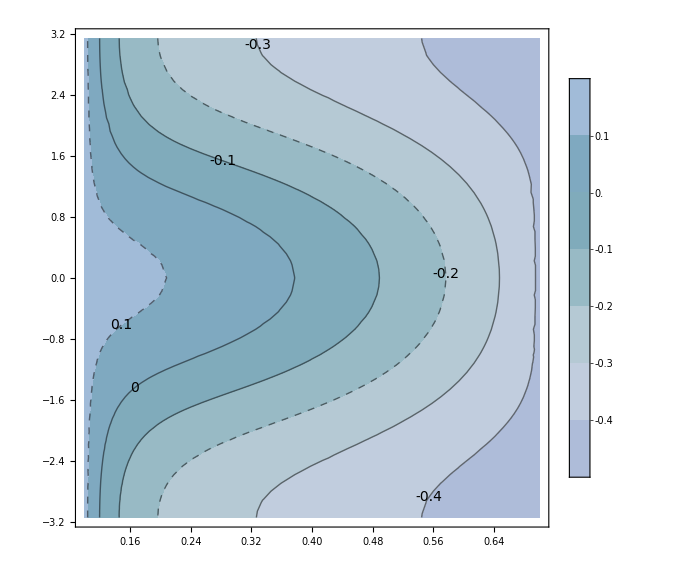

```mathematica
ContourPlot[1/S^2(0.0021657737272126763580658023805609767722461568944272772189593698591752691333`47.63468230432651-0.07615220735673374867901057821451805214388291452307378557444918444084486761765`47.67211739586873 S^2-0.7142857142857142857142857142857142857142857142857142857143`47.78421587635253 S^4+0.23809523809523809523809523809523809523809523809523809523809523809523809523809`47.67211739586873 √(-0.12994642363276058148394814283365860633476941366563663313756219155051614799804`48.71777081980522+1.4`48.71777081980522 S-1.`48.71777081980522 S^2) √(0.12994642363276058148394814283365860633476941366563663313756219155051614799804`48.71777081980522+1.4`48.71777081980522 S+S^2) √(-0.00489999999999999999999999999999999999999999999999999999999999999999999999999`47.57095051677566+0.5`47.74704177583134 S^2-1.`48.04807177149532 S^4) Cos[ϕ]),{S,Smin,Smax},{ϕ,-π,π},FrameLabel->{Style["",16],Style["",16]},ContourLabels->(Text[Style[#3,14],{#1,#2},Background->LightYellow]&),PlotLegends->Automatic,ColorFunction->"Aquamarine",ContourStyle->{Black,Black,Dashed},ImageSize->Large]
```

```mathematica
S1=(S1 /.sol0[[1]])  ;
S2=(S2 /.sol0[[1]])   ;
L=(L /.sol0[[1]])  ;
S = S1[t]+S2[t];
J = L[t]+S1[t]+S2[t];
```

```mathematica
zcap = J/Norm[J]  ; 
xcap = (L[t]-zcap.L[t]  zcap)/Norm[L[t]-zcap.L[t]  zcap]; 
ycap = Cross[zcap,xcap];
```

```mathematica
Sperp = Cross[ycap,  S1[t]+S2[t]] ; 
SperpNorm = Sperp/Norm[Sperp] ; 
S1norm = S1[t]/Norm[S1[t]] ;
Snorm = S/Norm[S] ;
```

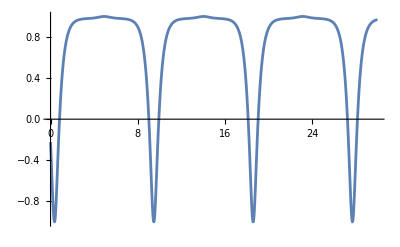

```mathematica
Plot[ (S1norm.SperpNorm)/Norm[Cross[S1norm, Snorm]] ,{t,0,30},PlotRange->All]
```